```mathematica
c=299792458.;
ℏ=1.0545718*10^-34;
f770=3.892596*10^14;
f680=c/(680*10^-9);
f578=c/(578*10^-9);
Γ399=2*π*30.*10^6;
Γ556=2*π*180.*10^3;
Γ770=3.7*10^7;
Γ680=2.7*10^7;
Γ578=2π*6.*10^-3;
Isat399=600;
Isat556=1.39;
Isat578=(ℏ(2π*f578)^3)/(4π c^2)Γ578
Isat770=(ℏ(2π*f770)^3)/(4π c^2)Γ770
Isat680=(ℏ(2π*f680)^3)/(4π c^2)Γ680
```

1.21836×10^-7

50.5457

53.5875

### scattering rate

```mathematica
ρee=1/2 s/(1+((2Δ)/Γ)^2+s);
Rsc=Γ ρee;
```

```mathematica
Rsc/.{s->64,Δ->2π*2.0*10^6,Γ->Γ556}
```

64762.7

```mathematica
Rsc/.{s->32,Δ->2π*2.0*10^6,Γ->Γ556}
```

34348.2

```mathematica
Rsc/.{s->0.006,Δ->2π*0.0*10^6,Γ->Γ399}
```

562114.

### intensity / saturation

```mathematica
Isat399=600;
Isat556=1.39;
I0=(2*P0)/(π w0^2);
```

```mathematica
I0/Isat556/.{P0->220.*10^-6,w0->2.5/2*10^-3}
```

64.4864

```mathematica
I0/Isat556/.{P0->50*10^-6,w0->0.6*10^-3}
```

63.6111

```mathematica
I0/Isat399/.{P0->1.7*10^-6,w0->0.5394*10^-3}
```

0.00619949

```mathematica
I0/.{P0->1.787*10^-6,w0->0.5394*10^-3}
```

3.91005

```mathematica
I0/Isat770/.{P0->4.8*10^-3,w0->0.6*10^-3}
```

167.932

```mathematica
I0/Isat680/.{P0->6*10^-3,w0->460.*10^-9}
```

3.36862×10^8

```mathematica
I0/Isat578/.{P0->6*10^-3,w0->460.*10^-9}
```

1.48164×10^17

```mathematica
Γ770/(2π)
```

5.88873×10^6

### rabi rate

```mathematica
Ω=Γ √(s/2*(1+((2*Δ)/Γ)^2));
```

```mathematica
Ω0=Ω/.{Γ->Γ770,s->167.,Δ->0};
 Ω0/(2π)
```

5.38103×10^7

```mathematica
Rsc399[s_]:=Rsc/.{Δ->2π*0.0*10^6,Γ->Γ399}
```

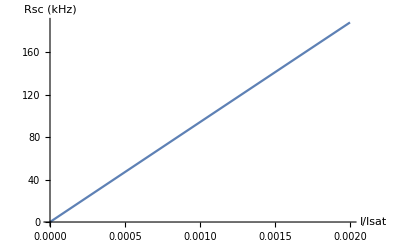

```mathematica
Plot[Rsc399[s]/10^3,{s,0,2*10^-3},AxesLabel->{"I/Isat","Rsc (kHz)"}]
```

## beam size

```mathematica
w=(λ f)/(π w0);
```

```mathematica
w/.{λ->556.*10^-9,f->0.011,w0->3.*10^-6}
```

0.000648928

```mathematica
45/(55/60.)^2
```

53.5537

## light shift Z

```mathematica
Ip=I0/.{w0->10.^-3,P0->0.4*10^-3};
Ωp=Γ556 √(Ip/(2 Isat556));
Δp=2π 5.*10^6;
ωs=Ωp^2/(4 Δp);
Rscp=Rsc/.{s->Ip/Isat556,Δ->Δp,Γ->Γ556}
ωs/(2π)
```

183.2

31675.1

148392.

```mathematica
Ip/Isat556
((2Δp)/Γ556)^2
```

183.2

3086.42